```mathematica
Assuming[z<1,Series[z^h Hypergeometric2F1[h,h,2h,z],{z,1,0}]]
```

-(Gamma[2 h] (2 EulerGamma+Log[1-z]+2 PolyGamma[0,h]))/Gamma[h]^2+O[z-1]^1

```mathematica
Assuming[z<1,Series[z^h Hypergeometric2F1[h,h,2h,z],{z,1,0}]]
```

-(Gamma[2 h] (2 EulerGamma+Log[1-z]+2 PolyGamma[0,h]))/Gamma[h]^2+O[z-1]^1

```mathematica
Integrate[Sin[x]^n,x]
```

-Cos[x] Hypergeometric2F1[1/2,(1-n)/2,3/2,Cos[x]^2] Sin[x]^(1+n) (Sin[x]^2)^(1/2 (-1-n))

```mathematica
Integrate[Sin[x]^(d-p-2),x]//FullSimplify
```

(√(Cos[x]^2) Hypergeometric2F1[1/2,1/2 (-1+d-p),1/2 (1+d-p),Sin[x]^2] Sec[x] Sin[x]^(-1+d-p))/(-1+d-p)

```mathematica
Assuming[d>1+p,Limit[(Hypergeometric2F1[1/2,1/2 (-1+d-p),1/2 (1+d-p),Sin[x]^2] Sin[x]^(-1+d-p))/(-1+d-p)/.d->4/.p->1,x->0]]
Assuming[d>1+p,Limit[(Hypergeometric2F1[1/2,1/2 (-1+d-p),1/2 (1+d-p),Sin[x]^2] Sin[x]^(-1+d-p))/(-1+d-p)/.d->4/.p->1,x->Pi]]
```

0

0

```mathematica
(Hypergeometric2F1[1/2,1/2 (-1+d-p),1/2 (1+d-p),x^2] x^(-1+d-p))/(-1+d-p)/.d->4/.p->1
```

1-√(1-x^2)

```mathematica
ComplexPlot[1-√(1-x^2),{x,-5-5I,5+5I}]
```

-Graphics-

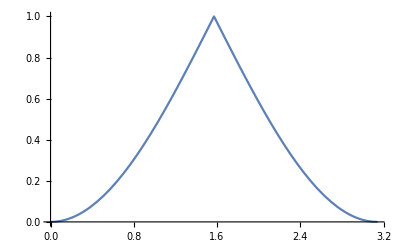

```mathematica
Plot[1-√(1-Sin[x]^2),{x,0,Pi}]
```

```mathematica
Integrate[4/((r^2+1)^2)r^(n-1),r]
Integrate[Sin[x]^(n-1),x]//FullSimplify
```

(4 r^n Hypergeometric2F1[2,n/2,1+n/2,-r^2])/n

(√(Cos[x]^2) Hypergeometric2F1[1/2,n/2,(2+n)/2,Sin[x]^2] Sec[x] Sin[x]^n)/n

```mathematica
Series[DedekindEta[I t],{t,0,1}]
```

ⅇ^(-π/(12 t)+O[t]^2) (1/(√t)+O[t]^(3/2))

```mathematica
Series[Beta[1-u,-1-s],{s,0,0}]
Series[Beta[1-t,-1-s],{s,0,0}]
```

-u/s-u (-1+EulerGamma+PolyGamma[0,-u])+O[s]^1

-t/s-t (-1+EulerGamma+PolyGamma[0,-t])+O[s]^1

```mathematica
-Sin[x]^2 (-Csc[x]^2+Csc[x]^2 √((-1+Csc[x]^2) Sin[x]^2))/.x->Pi/2-0.0001
```

0.9999

```mathematica
(1/2(1-2))(-1/24)
```

1/48

```mathematica
(*NS:*)
-1/24 8-8/48
(*R:*)
-1/24 8+8/24
```

-1/2

0

```mathematica
(*NN:*)
(*Boson Hilbert Space*)
1/2 Zeta[-1]
(*Fermion Hilbert Space*)
-1/48
(*DD:*)
(*Boson Hilbert Space*)
1/2 Zeta[-1]
(*Fermion Hilbert Space*)
-1/48
(*ND*)
(*Boson Hilbert Space*)
1/2 1/2(Zeta[-1]-2Zeta[-1])
(*Fermion Hilbert Space*)
1/16-1/48
```

-1/24

-1/48

-1/24

-1/48

1/48

1/24

```mathematica
1/((q^(1/24))^8)1/((q^(1/24))^4)Sqrt[q^(1/8)]
```

1/q^(7/16)

```mathematica
1/24
```

```mathematica
-1/4(1-2)Zeta[-1]
```

-1/48

```mathematica
(-1/24-1/48)
```

-1/16